```mathematica
a=0;b=1;
```

peak[x_] = Piecewise[{{h - Abs[x - t - h], t <= x <= t + 2 h}}, 0]

D[peak[x], x]

t = 0.5; h = 0.1; Plot[peak[x], {x, a, b}, AspectRatio -> 1, PlotRange -> Full]

Clear[t, h]

```mathematica
bump[x_]=Piecewise[{{(x-t)^3/6,t≤x≤t+h},{((x-t)^2(t+2h-x)+(x-t)(t+3h-x)(x-t-h)+(t+4h-x)(x-t-h)^2)/6,t+h≤x≤t+2h},{((x-t)(t+3h-x)^2+(t+4h-x)(x-t-h)(t+3h-x)+(t+4h-x)^2(x-t-2h))/6,t+2h≤x≤t+3h},{(t+4h-x)^3/6,t+3h≤x≤t+4h}},0]
```

Piecewise[{{1/6 (-t+x)^3, t≤x≤h+t}, {1/6 ((2 h+t-x) (-t+x)^2+(3 h+t-x) (-t+x) (-h-t+x)+(4 h+t-x) (-h-t+x)^2), h+t≤x≤2 h+t}, {1/6 ((3 h+t-x)^2 (-t+x)+(4 h+t-x)^2 (-2 h-t+x)+(3 h+t-x) (4 h+t-x) (-h-t+x)), 2 h+t≤x≤3 h+t}, {1/6 (4 h+t-x)^3, 3 h+t≤x≤4 h+t}, {0, True}}]

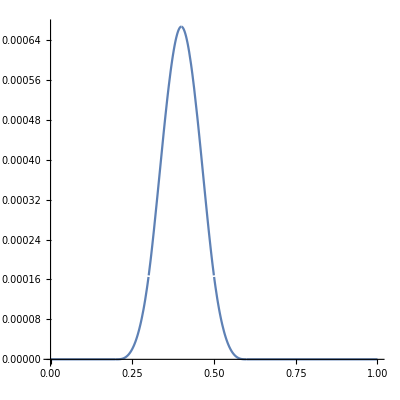

```mathematica
t=0.2;h=0.1;Plot[bump[x],{x,a,b},AspectRatio->1,PlotRange->Full]
```

```mathematica
Clear[t,h]
```

```mathematica
b1[x_]=(x-t)^3/6
```

1/6 (-t+x)^3

```mathematica
b2[x_]=((x-t)^2(t+2h-x)+(x-t)(t+3h-x)(x-t-h)+(t+4h-x)(x-t-h)^2)/6
```

1/6 ((2 h+t-x) (-t+x)^2+(3 h+t-x) (-t+x) (-h-t+x)+(4 h+t-x) (-h-t+x)^2)

```mathematica
b3[x_]=((x-t)(t+3h-x)^2+(t+4h-x)(x-t-h)(t+3h-x)+(t+4h-x)^2(x-t-2h))/6
```

1/6 ((3 h+t-x)^2 (-t+x)+(4 h+t-x)^2 (-2 h-t+x)+(3 h+t-x) (4 h+t-x) (-h-t+x))

```mathematica
b4[x_]=(t+4h-x)^3/6
```

1/6 (4 h+t-x)^3

```mathematica
0==b1[t]
```

True

```mathematica
b1[t+h]==b2[t+h]
```

True

```mathematica
b2[t+2h]==b3[t+2h]
```

True

```mathematica
b3[t+3h]==b4[t+3h]
```

True

```mathematica
b4[t+4h]==0
```

True

```mathematica
bumpp1[x_]=D[bump[x],x]
```

Piecewise[{{1/2 (-t+x)^2, t-x≤0&&h+t-x≥0}, {1/6 (2 (2 h+t-x) (-t+x)+(3 h+t-x) (-t+x)-(-t+x)^2+(3 h+t-x) (-h-t+x)+2 (4 h+t-x) (-h-t+x)-(-t+x) (-h-t+x)-(-h-t+x)^2), h+t-x≤0&&2 h+t-x≥0}, {1/6 ((3 h+t-x)^2+(3 h+t-x) (4 h+t-x)+(4 h+t-x)^2-2 (3 h+t-x) (-t+x)-2 (4 h+t-x) (-2 h-t+x)-(3 h+t-x) (-h-t+x)-(4 h+t-x) (-h-t+x)), 2 h+t-x≤0&&3 h+t-x≥0}, {-1/2 (4 h+t-x)^2, 3 h+t-x≤0&&4 h+t-x≥0}, {0, True}}]

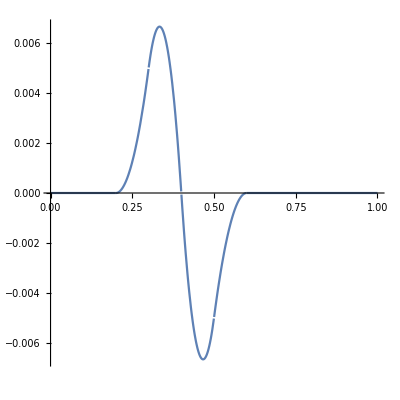

```mathematica
t=0.2;h=0.1;Plot[bumpp1[x],{x,a,b},AspectRatio->1,PlotRange->Full]
```

```mathematica
Clear[t,h]
```

```mathematica
b1p1[x_]=D[b1[x],x]
```

1/2 (-t+x)^2

```mathematica
b2p1[x_]=D[b2[x],x]
```

1/6 (2 (2 h+t-x) (-t+x)+(3 h+t-x) (-t+x)-(-t+x)^2+(3 h+t-x) (-h-t+x)+2 (4 h+t-x) (-h-t+x)-(-t+x) (-h-t+x)-(-h-t+x)^2)

```mathematica
b3p1[x_]=D[b3[x],x]
```

1/6 ((3 h+t-x)^2+(3 h+t-x) (4 h+t-x)+(4 h+t-x)^2-2 (3 h+t-x) (-t+x)-2 (4 h+t-x) (-2 h-t+x)-(3 h+t-x) (-h-t+x)-(4 h+t-x) (-h-t+x))

```mathematica
b4p1[x_]=D[b4[x],x]
```

-1/2 (4 h+t-x)^2

```mathematica
0==b1p1[t]
```

True

```mathematica
b1p1[t+h]==b2p1[t+h]
```

True

```mathematica
b2p1[t+2h]==b3p1[t+2h]
```

True

```mathematica
b3p1[t+3h]==b4p1[t+3h]
```

True

```mathematica
b4p1[t+4h]==0
```

True

```mathematica
bumpp2[x_]=D[bumpp1[x],x]
```

Piecewise[{{-t+x, t-x≤0&&h+t-x≥0}, {1/6 (8 h+6 t+2 (2 h+t-x)+2 (4 h+t-x)-6 x-4 (-t+x)-4 (-h-t+x)), h+t-x≤0&&2 h+t-x≥0}, {1/6 (-16 h-6 t-4 (3 h+t-x)-4 (4 h+t-x)+6 x+2 (-t+x)+2 (-2 h-t+x)), 2 h+t-x≤0&&3 h+t-x≥0}, {4 h+t-x, 3 h+t-x≤0&&4 h+t-x≥0}, {0, True}}]

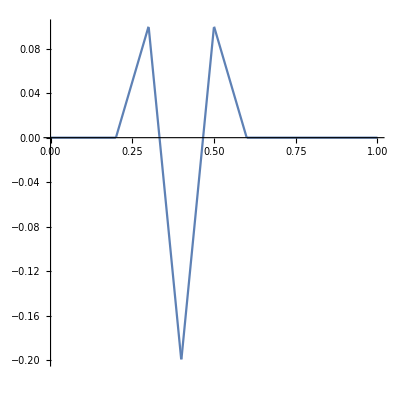

```mathematica
t=0.2;h=0.1;Plot[bumpp2[x],{x,a,b},AspectRatio->1,PlotRange->Full]
```

```mathematica
Clear[t,h]
```

```mathematica
b1p2[x_]=D[b1p1[x],x]
```

-t+x

```mathematica
b2p2[x_]=D[b2p1[x],x]
```

1/6 (8 h+6 t+2 (2 h+t-x)+2 (4 h+t-x)-6 x-4 (-t+x)-4 (-h-t+x))

```mathematica
b3p2[x_]=D[b3p1[x],x]
```

1/6 (-16 h-6 t-4 (3 h+t-x)-4 (4 h+t-x)+6 x+2 (-t+x)+2 (-2 h-t+x))

```mathematica
b4p2[x_]=D[b4p1[x],x]
```

4 h+t-x

```mathematica
0==b1p2[t]
```

True

```mathematica
b1p2[t+h]==Simplify[b2p2[t+h]]
```

True

```mathematica
Simplify[b2p2[t+2h]]==Simplify[b3p2[t+2h]]
```

True

```mathematica
Simplify[b3p2[t+3h]]==Simplify[b4p2[t+3h]]
```

True

```mathematica
b4p2[t+4h]==0
```

True

```mathematica
Clear[t,h]
```

```mathematica
bumpp3[x_]=D[bumpp2[x],x]
```

Piecewise[{{1, t-x≤0&&h+t-x≥0}, {-3, h+t-x≤0&&2 h+t-x≥0}, {3, 2 h+t-x≤0&&3 h+t-x≥0}, {-1, 3 h+t-x≤0&&4 h+t-x≥0}, {0, True}}]

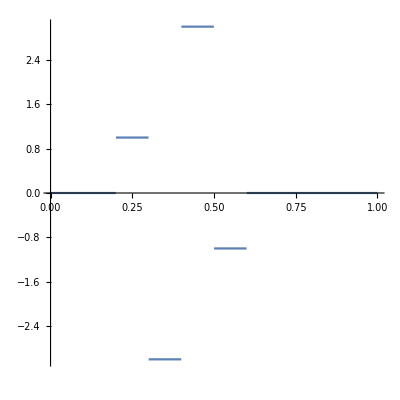

```mathematica
t=0.2;h=0.1;Plot[bumpp3[x],{x,a,b},AspectRatio->1,PlotRange->Full]
```

```mathematica
Clear[t,h]
```

```mathematica
b1p3[x_]=D[b1p2[x],x]
```

1

```mathematica
b2p3[x_]=D[b2p2[x],x]
```

-3

```mathematica
b3p3[x_]=D[b3p2[x],x]
```

3

```mathematica
b4p3[x_]=D[b4p2[x],x]
```

-1

```mathematica
bump[x_]=Piecewise[{{(x-t)^3/6,t≤x≤t+h},{((x-t)^2(t+2h-x)+(x-t)(t+3h-x)(x-t-h)+(t+4h-x)(x-t-h)^2)/6,t+h≤x≤t+2h},{((x-t)(t+3h-x)^2+(t+4h-x)(x-t-h)(t+3h-x)+(t+4h-x)^2(x-t-2h))/6,t+2h≤x≤t+3h},{(t+4h-x)^3/6,t+3h≤x≤t+4h}},0]
```

Piecewise[{{1/6 (-t+x)^3, t≤x≤h+t}, {1/6 ((2 h+t-x) (-t+x)^2+(3 h+t-x) (-t+x) (-h-t+x)+(4 h+t-x) (-h-t+x)^2), h+t≤x≤2 h+t}, {1/6 ((3 h+t-x)^2 (-t+x)+(4 h+t-x)^2 (-2 h-t+x)+(3 h+t-x) (4 h+t-x) (-h-t+x)), 2 h+t≤x≤3 h+t}, {1/6 (4 h+t-x)^3, 3 h+t≤x≤4 h+t}, {0, True}}]

Integrate[bump[x], {x, a, b}, Assumptions -> a ∈ Reals && b ∈ Reals]

```mathematica
Integrate[bump[x],{x,t,t+4h}]
```

Integrate::pwrl: Unable to prove that integration limits {t,4 h+t} are real. Adding assumptions may help.

∫_t^(4 h+t) (Piecewise[{{1/6 (-t+x)^3, t≤x≤h+t}, {1/6 ((2 h+t-x) (-t+x)^2+(3 h+t-x) (-t+x) (-h-t+x)+(4 h+t-x) (-h-t+x)^2), h+t≤x≤2 h+t}, {1/6 ((3 h+t-x)^2 (-t+x)+(4 h+t-x)^2 (-2 h-t+x)+(3 h+t-x) (4 h+t-x) (-h-t+x)), 2 h+t≤x≤3 h+t}, {1/6 (4 h+t-x)^3, 3 h+t≤x≤4 h+t}, {0, True}}])ⅆx

```mathematica
intbump[x_]=Integrate[bump[x],x]
```

Piecewise[{{1/24 (-t+x)^4, t-x≤0&&h+t-x≥0}, {(2 h^3 x)/3+2 h^2 t x+2 h t^2 x+(t^3 x)/2-h^2 x^2-2 h t x^2-(3 t^2 x^2)/4+(2 h x^3)/3+(t x^3)/2-x^4/8, h+t-x≤0&&2 h+t-x≥0}, {-(22 h^3 x)/3-10 h^2 t x-4 h t^2 x-(t^3 x)/2+5 h^2 x^2+4 h t x^2+(3 t^2 x^2)/4-(4 h x^3)/3-(t x^3)/2+x^4/8, 2 h+t-x≤0&&3 h+t-x≥0}, {-1/24 (4 h+t-x)^4, 3 h+t-x≤0&&4 h+t-x≥0}, {0, True}}]

```mathematica
Integrate[b1[x],{x,t,t+h}]+Integrate[b2[x],{x,t+h,t+2h}]+Integrate[b3[x],{x,t+2h,t+3h}]+Integrate[b4[x],{x,t+3h,t+4h}]
```

h^4

```mathematica
Simplify[bump[x]]
```

Piecewise[{{1/6 (-t+x)^3, t≤x≤h+t}, {(2 h^3)/3+2 h^2 (t-x)+2 h (t-x)^2+1/2 (t-x)^3, h+t≤x≤2 h+t}, {-(22 h^3)/3-10 h^2 (t-x)-4 h (t-x)^2-1/2 (t-x)^3, 2 h+t≤x≤3 h+t}, {1/6 (4 h+t-x)^3, 3 h+t≤x≤4 h+t}, {0, True}}]

```mathematica
showbump[x_,t_,h_]=Piecewise[{{(x-t)^3/6,t≤x≤t+h},{((x-t)^2(t+2h-x)+(x-t)(t+3h-x)(x-t-h)+(t+4h-x)(x-t-h)^2)/6,t+h≤x≤t+2h},{((x-t)(t+3h-x)^2+(t+4h-x)(x-t-h)(t+3h-x)+(t+4h-x)^2(x-t-2h))/6,t+2h≤x≤t+3h},{(t+4h-x)^3/6,t+3h≤x≤t+4h}},0]
```

Piecewise[{{1/6 (-t+x)^3, t≤x≤h+t}, {1/6 ((2 h+t-x) (-t+x)^2+(3 h+t-x) (-t+x) (-h-t+x)+(4 h+t-x) (-h-t+x)^2), h+t≤x≤2 h+t}, {1/6 ((3 h+t-x)^2 (-t+x)+(4 h+t-x)^2 (-2 h-t+x)+(3 h+t-x) (4 h+t-x) (-h-t+x)), 2 h+t≤x≤3 h+t}, {1/6 (4 h+t-x)^3, 3 h+t≤x≤4 h+t}, {0, True}}]

```mathematica
c[h_]=1.5/(1-h/0.1)
```

1.5/(1-10. h)

```mathematica
twobp[x_,t_,h_]=showbump[x,0,0.1]+15(c[h]-1)/16*showbump[x,t,h]
```

(Piecewise[{{x^3/6, 0≤x≤0.1}, {1/6 ((0.4-x) (-0.1+x)^2+(0.3-x) (-0.1+x) x+(0.2-x) x^2), 0.1≤x≤0.2}, {1/6 ((0.4-x)^2 (-0.2+x)+(0.3-x) (0.4-x) (-0.1+x)+(0.3-x)^2 x), 0.2≤x≤0.3}, {1/6 (0.4-x)^3, 0.3≤x≤0.4}, {0, True}}])+15/16 (-1+1.5/(1-10. h)) (Piecewise[{{1/6 (-t+x)^3, t≤x≤h+t}, {1/6 ((2 h+t-x) (-t+x)^2+(3 h+t-x) (-t+x) (-h-t+x)+(4 h+t-x) (-h-t+x)^2), h+t≤x≤2 h+t}, {1/6 ((3 h+t-x)^2 (-t+x)+(4 h+t-x)^2 (-2 h-t+x)+(3 h+t-x) (4 h+t-x) (-h-t+x)), 2 h+t≤x≤3 h+t}, {1/6 (4 h+t-x)^3, 3 h+t≤x≤4 h+t}, {0, True}}])

```mathematica
showtwobp[x_]=twobp[x,0.5,0.05]
```

1.875 (Piecewise[{{1/6 (-0.5+x)^3, 0.5≤x≤0.55}, {1/6 ((0.7-x) (-0.55+x)^2+(0.65-x) (-0.55+x) (-0.5+x)+(0.6-x) (-0.5+x)^2), 0.55≤x≤0.6}, {1/6 ((0.7-x)^2 (-0.6+x)+(0.65-x) (0.7-x) (-0.55+x)+(0.65-x)^2 (-0.5+x)), 0.6≤x≤0.65}, {1/6 (0.7-x)^3, 0.65≤x≤0.7}, {0, True}}])+(Piecewise[{{x^3/6, 0≤x≤0.1}, {1/6 ((0.4-x) (-0.1+x)^2+(0.3-x) (-0.1+x) x+(0.2-x) x^2), 0.1≤x≤0.2}, {1/6 ((0.4-x)^2 (-0.2+x)+(0.3-x) (0.4-x) (-0.1+x)+(0.3-x)^2 x), 0.2≤x≤0.3}, {1/6 (0.4-x)^3, 0.3≤x≤0.4}, {0, True}}])

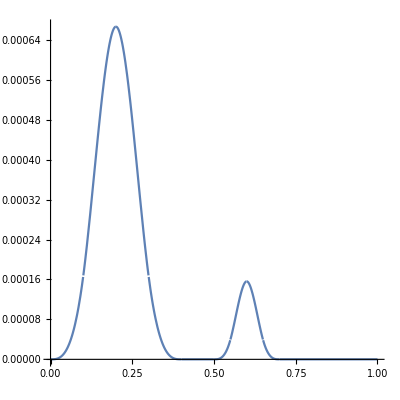

```mathematica
Plot[showtwobp[x],{x,0,1},AspectRatio->1,PlotRange->Full]
```